## Mathematica code to calculate the beam waist size and location for power measurements at two distances with the knife edge technique

```mathematica
(*ImportString["copied-data-from-excel","List"]*)
(*uncomment the first line to produce the appropriate list of values after you copy them from excel*)
```

```mathematica
(*For example, this is copied data from a column in Excel consisting of values:*)
ImportString["10
10.25
10.5
10.75
11
11.25
11.5
11.75
12
", "List"]
(*then you copy the result (the output below) and paste it in the appropriate input data below, e.g. at powerpointsfirstdistance = ... . You can do this for all.*)
```

{10,10.25,10.5,10.75,11,11.25,11.5,11.75,12}

The number of knife edge distance points and power points is the same for the first distance: True

The number of knife edge distance points and power points is the same for the second distance: True

The list plot:

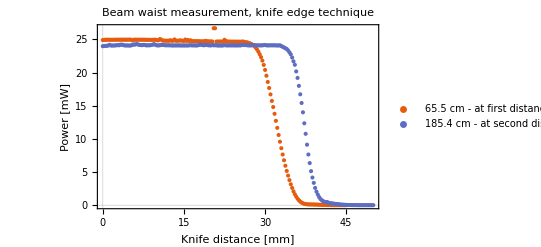

The line plot:

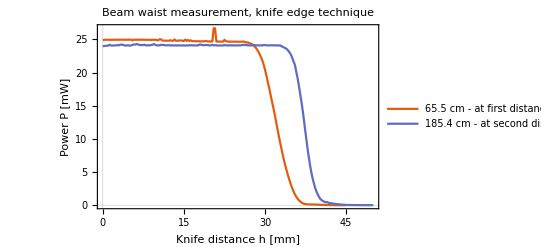

The fitting parameters for the power vs knife edge distance measurement at first distance z turn out to be: amplitude→24.8683 mW, center→32.077 mm, width→4.608 mm

The fitting parameters for the power vs knife edge distance measurement at second distance z turn out to be: amplitude→24.1112 mW, center→37.2883 mm, width→3.1622 mm

Both fitted plots and both list plots together:

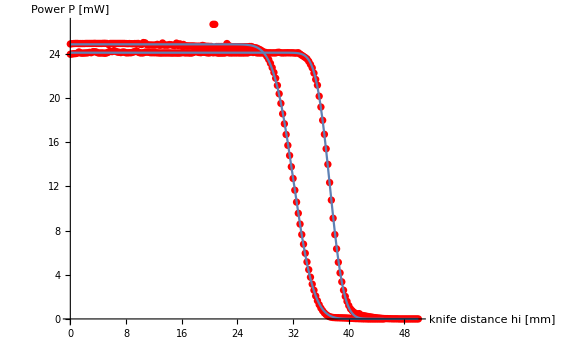

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

First solution: Minimum waist is w0→0.052266 mm  at z0→1366.07 mm

Second solution: Minimum waist is w0→0.28011 mm  at z0→4459.04 mm

Plotting the two solutions:

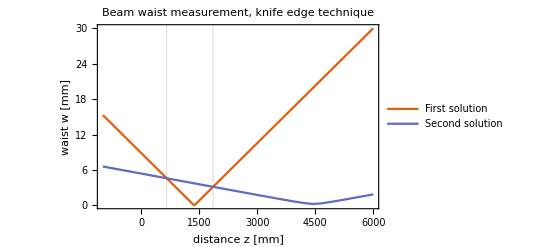

```mathematica
(*Text in pink background is where INPUT is expected. Text in blue background is what is gonna come out as OUTPUT.*)

(*---------------Insert the data----------------*)

firstdistance(*mm*)=65.5 10(*mm*); (*this is your first distance from the reference point to where the knife edge is*)
seconddistance(*mm*)=185.4 10(*mm*);(*this is your second distance from the reference point to where the knife edge is*)
knifedistancepointsleft(*mm*)={0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,2.75,3,3.25,3.5,3.75,4,4.25,4.5,4.75,5,5.25,5.5,5.75,6,6.25,6.5,6.75,7,7.25,7.5,7.75,8,8.25,8.5,8.75,9,9.25,9.5,9.75,10,10.25,10.5,10.75,11,11.25,11.5,11.75,12,12.25,12.5,12.75,13,13.25,13.5,13.75,14,14.25,14.5,14.75,15,15.25,15.5,15.75,16,16.25,16.5,16.75,17,17.25,17.5,17.75,18,18.25,18.5,18.75,19,19.25,19.5,19.75,20,20.25,20.5,20.75,21,21.25,21.5,21.75,22,22.25,22.5,22.75,23,23.25,23.5,23.75,24,24.25,24.5,24.75,25,25.25,25.5,25.75,26,26.25,26.5,26.75,27,27.25,27.5,27.75,28,28.25,28.5,28.75,29,29.25,29.5,29.75,30,30.25,30.5,30.75,31,31.25,31.5,31.75,32,32.25,32.5,32.75,33,33.25,33.5,33.75,34,34.25,34.5,34.75,35,35.25,35.5,35.75,36,36.25,36.5,36.75,37,37.25,37.5,37.75,38,38.25,38.5,38.75,39,39.25,39.5,39.75,40,40.25,40.5,40.75,41,41.25,41.5,41.75,42,42.25,42.5,42.75,43,43.25,43.5,43.75,44,44.25,44.5,44.75,45}(*mm*);(*these are the knife edge distances, slowly covering the beam at the first distance (I also call it left distance)*)
knifedistancepointsright(*mm*)={0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,2.75,3,3.25,3.5,3.75,4,4.25,4.5,4.75,5,5.25,5.5,5.75,6,6.25,6.5,6.75,7,7.25,7.5,7.75,8,8.25,8.5,8.75,9,9.25,9.5,9.75,10,10.25,10.5,10.75,11,11.25,11.5,11.75,12,12.25,12.5,12.75,13,13.25,13.5,13.75,14,14.25,14.5,14.75,15,15.25,15.5,15.75,16,16.25,16.5,16.75,17,17.25,17.5,17.75,18,18.25,18.5,18.75,19,19.25,19.5,19.75,20,20.25,20.5,20.75,21,21.25,21.5,21.75,22,22.25,22.5,22.75,23,23.25,23.5,23.75,24,24.25,24.5,24.75,25,25.25,25.5,25.75,26,26.25,26.5,26.75,27,27.25,27.5,27.75,28,28.25,28.5,28.75,29,29.25,29.5,29.75,30,30.25,30.5,30.75,31,31.25,31.5,31.75,32,32.25,32.5,32.75,33,33.25,33.5,33.75,34,34.25,34.5,34.75,35,35.25,35.5,35.75,36,36.25,36.5,36.75,37,37.25,37.5,37.75,38,38.25,38.5,38.75,39,39.25,39.5,39.75,40,40.25,40.5,40.75,41,41.25,41.5,41.75,42,42.25,42.5,42.75,43,43.25,43.5,43.75,44,44.25,44.5,44.75,45,45.25,45.5,45.75,46,46.25,46.5,46.75,47,47.25,47.5,47.75,48,48.25,48.5,48.75,49,49.25,49.5,49.75,50}(*mm*);(*these are the knife edge distances, slowly covering the beam at the second distance (I also call it right distance)*)
powerpointsfirstdistance(*mW*)={24.9,24.93,24.94,24.95,24.95,24.94,24.94,24.94,24.94,24.95,24.95,24.95,24.95,24.95,24.96,24.95,24.95,24.95,24.95,24.96,24.96,24.95,24.85,24.95,24.95,24.95,24.95,24.95,24.95,24.95,24.95,24.95,24.94,24.93,24.94,24.93,24.92,24.94,24.94,24.95,24.88,24.85,25.03,25.,24.84,24.81,24.81,24.8,24.8,24.8,24.87,24.79,24.79,24.99,24.79,24.81,24.79,24.85,24.83,24.78,24.77,24.98,24.76,24.91,24.75,24.86,24.74,24.73,24.72,24.72,24.72,24.72,24.7,24.7,24.7,24.7,24.77,24.72,24.69,24.69,24.68,24.68,26.68,26.68,24.67,24.67,24.67,24.67,24.67,24.66,24.94,24.74,24.69,24.66,24.66,24.66,24.65,24.66,24.65,24.65,24.65,24.65,24.64,24.67,24.67,24.6,24.56,24.54,24.46,24.39,24.29,24.16,23.98,23.76,23.49,23.15,22.76,22.32,21.8,21.15,20.39,19.52,18.58,17.67,16.7,15.72,14.8,13.78,12.72,11.66,10.58,9.57,8.59,7.64,6.77,5.95,5.16,4.46,3.78,3.15,2.6,2.08,1.65,1.29,0.98,0.74,0.54,0.39,0.28,0.2,0.16,0.13,0.12,0.11,0.11,0.1,0.1,0.09,0.09,0.08,0.07,0.06,0.05,0.04,0.03,0.03,0.02,0.02,0.01,0.01,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}(*mW*);(*these are the measurements that the power meter shows when moving the knife edge at the first distance away from the reference point*)
powerpointsseconddistance(*mW*)={23.97,24,24.02,24.03,24.07,24.18,24.08,24.07,24.08,24.09,24.1,24.14,24.11,24.2,24.2,24.17,24.09,24.08,24.09,24.08,24.06,24.1,24.17,24.24,24.21,24.3,24.24,24.17,24.15,24.12,24.17,24.17,24.1,24.1,24.11,24.11,24.16,24.21,24.29,24.16,24.1,24.09,24.1,24.17,24.16,24.16,24.11,24.11,24.11,24.11,24.1,24.09,24.08,24.09,24.09,24.09,24.09,24.09,24.08,24.08,24.09,24.08,24.08,24.08,24.11,24.12,24.09,24.1,24.09,24.08,24.09,24.15,24.24,24.17,24.13,24.11,24.16,24.15,24.12,24.09,24.09,24.18,24.1,24.12,24.11,24.07,24.08,24.08,24.08,24.09,24.14,24.1,24.09,24.09,24.1,24.09,24.1,24.09,24.09,24.09,24.09,24.1,24.09,24.15,24.19,24.13,24.18,24.1,24.09,24.09,24.09,24.15,24.15,24.09,24.1,24.1,24.09,24.1,24.09,24.14,24.15,24.1,24.09,24.1,24.1,24.11,24.1,24.1,24.1,24.08,24.08,24.11,23.99,23.88,23.78,23.67,23.55,23.33,23.05,22.74,22.26,21.69,21.17,20.17,19.19,17.99,16.72,15.41,14.,12.35,10.76,9.12,7.64,6.35,5.13,4.17,3.36,2.6,2.04,1.59,1.21,0.91,0.74,0.59,0.5,0.43,0.48,0.34,0.31,0.28,0.25,0.22,0.19,0.17,0.14,0.12,0.1,0.08,0.07,0.05,0.04,0.03,0.03,0.02,0.02,0.01,0.01,0.01,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}(*mW*);(*these are the measurements that the power meter shows when moving the knife edge at the second distance away from the reference point*)


(*----------------Calculation------------------*)


maximumknifeedgedistanceleft=knifedistancepointsleft[[Length[knifedistancepointsleft]]](*mm*);
maximumknifeedgedistanceright=knifedistancepointsright[[Length[knifedistancepointsright]]](*mm*);
(*save for later, when the time to plot comes*)

Print["
The number of knife edge distance points and power points is the same for the first distance: ",Length[knifedistancepointsleft]==Length[powerpointsfirstdistance]]
Print["The number of knife edge distance points and power points is the same for the second distance: ",Length[knifedistancepointsright]==Length[powerpointsseconddistance]]
(*Sanity check: you should get True for both*)

(*Collect the knifedistancepoints and the powerpoints on a proper list consisting of pairs of values {{power1,knife1},{power2,knife2},...} so that they can be plotted*)
powerandknifedistancepairfirst=Inner[List,knifedistancepointsleft,powerpointsfirstdistance,List];
powerandknifedistancepairsecond=Inner[List,knifedistancepointsright,powerpointsseconddistance,List];
Print["
The list plot: "]
 powervsknifedistanceplots=ListPlot[{powerandknifedistancepairfirst,powerandknifedistancepairsecond},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Power [mW]"],None},{HoldForm["Knife distance [mm]"],None}},PlotLabel->HoldForm["Beam waist measurement, knife edge technique"],PlotLegends->{""firstdistance/10"cm - at first distance z",""seconddistance/10"cm - at second distance z"}]
(*this spits out the list plot for both sets of points, i.e. two lines showing the graph of power vs knife edge distance*)

Print["
The line plot: "]
powervsknifedistanceplots=ListLinePlot[{powerandknifedistancepairfirst,powerandknifedistancepairsecond},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Power P [mW]"],None},{HoldForm["Knife distance h [mm]"],None}},PlotLabel->HoldForm["Beam waist measurement, knife edge technique"],PlotLegends->{""firstdistance/10"cm - at first distance z",""seconddistance/10"cm - at second distance z"}]
(*this spits out the line plot for both sets of points*)

parametersleft=FindFit[powerandknifedistancepairfirst,{amplitude/2 Erfc[(hi-center)/(width/(√2))],{amplitude>=0,center>=0,width>=0}},{amplitude,center,width},hi];
Print["The fitting parameters for the power vs knife edge distance measurement at first distance z turn out to be: ",parametersleft[[1]]," mW, ",parametersleft[[2]]," mm, ",parametersleft[[3]]," mm "]
(*this spits out the parameters for the power vs first distance measurement fitting*)

parametersright=FindFit[powerandknifedistancepairsecond,{amplitude/2 Erfc[(hi-center)/(width/(√2))],{amplitude>=0,center>=0,width>=0}},{amplitude,center,width},hi];
(*this spits out the parameters for the power vs second distance measurement*)
Print["The fitting parameters for the power vs knife edge distance measurement at second distance z turn out to be: ",parametersright[[1]]," mW, ",parametersright[[2]]," mm, ",parametersright[[3]]," mm "]

Print["
Both fitted plots and both list plots together: "]
Show[ListPlot[powerandknifedistancepairfirst,PlotStyle->Red],ListPlot[powerandknifedistancepairsecond,PlotStyle->Red],Plot[1/2 amplitude Erfc[(hi-center)/(width/(√2))]/.parametersleft,{hi,0,maximumknifeedgedistanceleft}],Plot[1/2 amplitude Erfc[(hi-center)/(width/(√2))]/.parametersright,{hi,0,maximumknifeedgedistanceright}],PlotRange->Full,AxesLabel->{"knife distance hi [mm]","Power P [mW]"},ImageSize->Large]
(*this spits out both the fitted plots using the calculated parameters and the listplots*)

secondparameters=NSolve[{width==w0 Sqrt[1+((z-z0)/((π w0^2)/(1064*10^-6)))^2]/.{parametersleft[[3]],z->firstdistance}(*the first*),width==w0 Sqrt[1+((z-z0)/((π w0^2)/(1064*10^-6)))^2]/.{parametersright[[3]],z->seconddistance}(*the second*)},{w0,z0},Reals];
(*second pair of parameters; what we in fact started out to calculate*)
Print["
First solution: ","Minimum waist is ", secondparameters[[1,1]]," mm "," at ",secondparameters[[1,2]]," mm "]
Print["Second solution: ","Minimum waist is ", secondparameters[[2,1]]," mm ", " at ",secondparameters[[2,2]], " mm "]

(*Insert values for the z-axis; you pick them somewhat sensibly; just try things out, so that you see both minima*)
zminimum(*mm*)=-1000(*mm*);
zmaximum(*mm*)=6000(*mm*);
(*plot the two solutions*)
Print["
Plotting the two solutions: "]
waistvsdistanceplot=Plot[{w0 Sqrt[1+((z-z0)/((π w0^2)/(1064*10^-6)))^2]/.secondparameters[[1]],w0 Sqrt[1+((z-z0)/((π w0^2)/(1064*10^-6)))^2]/.secondparameters[[2]]},{z,zminimum,zmaximum},PlotTheme->"Scientific",FrameLabel->{{HoldForm["waist w [mm]"],None},{HoldForm["distance z [mm]"],None}},PlotLabel->HoldForm["Beam waist measurement, knife edge technique"],LabelStyle->{GrayLevel[0]},PlotLegends->{"First solution","Second solution"},GridLines->{{firstdistance,seconddistance},{}},PlotRange->All]
```